# Evaluation

BX Pan
2017.9.18

Cutting

```mathematica
S2SCut[polygon_,s2sdirectory_]:=Block[
{cpcprecip,cpclat,cpclon,cpctime,s2sprecip,s2slat,s2slon,s2stime,
 year=StringTake[StringCases[s2sdirectory,"_"~~__~~"-"],{2,5}][[1]],
 interval,
 points,indexes,cpcdirectory},
    cpcdirectory="/Users/lambda/Documents/Data/CPC_Precipitation/global/precip."<>year<>".nc";
	{cpcprecip,cpclat,cpclon,cpctime}=Map[Import[cpcdirectory,{"Datasets",#}]&,{"precip","lat","lon","time"}];
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[s2sdirectory,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
	interval=Map[Position[Abs[cpctime-#[s2stime]],Min[Abs[cpctime-#[s2stime]]]][[1,1]]&,{Min,Max}];	
    cpcprecip=Block[{DownScale,size},
        DownScale[data_,ratio_]:=Block[{convoluter},
			(* This Function performs spacial average downscaling of 2D data through uniform convolution ratio is kind like {5,4}*) 
			convoluter = Block[{net},
   			net = NetInitialize[ConvolutionLayer[1, ratio, "Stride" -> ratio, 
   						"Input" -> Flatten[{1, Dimensions[data]}]]];
               NetReplacePart[net, {"Weights" -> ConstantArray[1./(ratio/.List->Times), Flatten[{1, 1, ratio}]]}]];
            (convoluter@{data})[[1]]];
        size={Round[Abs[s2slat[[2]]-s2slat[[1]]]/Abs[cpclat[[2]]-cpclat[[1]]]],
          Round[Abs[s2slon[[2]]-s2slon[[1]]]/Abs[cpclon[[2]]-cpclon[[1]]]]};
        Map[DownScale[#,size]&,cpcprecip[[interval[[1]];;interval[[2]]]]]];
    points=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,points]];
    cpcprecip=Map[cpcprecip[[;;,#[[1]],#[[2]]]]&,indexes];
    s2sprecip=Block[{scale,offset,origion},
        {scale,offset}=Import[s2sdirectory,"Annotations"][[6,1;;2,2]];
        origin=Map[(s2sprecip[[;;,;;,#[[1]],#[[2]]]]*scale+offset)&,indexes];
        Transpose[Table[If[i==1,origin[[;;,1,;;]],origin[[;;,i,;;]]-origin[[;;,i-1,;;]]],{i,Dimensions[origin][[2]]}]]];
    {cpcprecip,s2sprecip,points}]
```

```mathematica
polygon=westconus[[1]];
s2sdirectory="/Users/lambda/Documents/Data/S2S/CMA/CMA_1994-01-01.nc";
(*s2sdirectory="/Users/lambda/Documents/Data/S2S/BoM/Bom_1981-01-01.nc";*)
```

```mathematica
{cpcprecip,s2sprecip,points}=S2SCut[polygon,s2sdirectory];
```

```mathematica
i=1;
Dimensions[s2sprecip[[;;,i+1,;;]]-s2sprecip[[;;,i,;;]]]
```

{13,32}

```mathematica
Dimensions[cpcprecip]
```

{33,60}

```mathematica
Dimensions[s2sprecip]
```

{33,60,3}

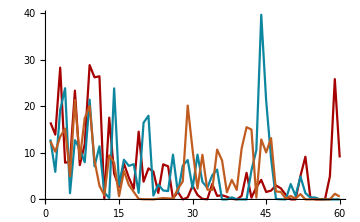
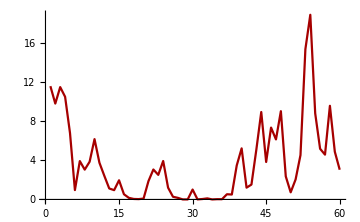

```mathematica
grid=3;
{ListLinePlot[Table[s2sprecip[[grid,;;,i]],{i,3}],PlotRange->Full,ImageSize->Medium],
 ListLinePlot[cpcprecip[[grid,;;]],PlotRange->Full,ImageSize->Medium]}
```